## From Riccardo:

```mathematica
(* Probs not needed *)
```

```mathematica
argumentLength[func_Symbol] := Lookup[SyntaxInformation[func], "ArgumentsPattern"]
argumentLength["Plot"]
```

## From Giulio and Tim:

### General:

```mathematica
WolframLanguageData["Exp","DocumentationExampleInputs"]
```

```mathematica
SyntaxInformation[Exp]
```

### Defined functions:

```mathematica
(* No longer useful *)
```

```mathematica
parseString[str_String]:=FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]];
```

```mathematica
flattenParse[exp_]:=Flatten@ReplaceRepeated[exp, RowBox[{anything___}]:>{anything}]
```

```mathematica
SetAttributes[makeExpressionString, {HoldFirst}]
makeExpressionString[exp_]:=StringTake[ToString[HoldComplete[exp], InputForm], {StringLength["HoldComplete["]+1,-StringLength["]"]-1}]
```

```mathematica
(*functionargs[function_]:=Length/@Map[Select[SyntaxInformation[function][[1,2]],#]&,{#==_&,#==_.&,#==OptionsPattern[]&}];*)
```

```mathematica
functionargs[function_String] := functionargs[Symbol[function]]
functionargs[function_Symbol]:=Length/@Map[Select[Lookup[SyntaxInformation[function], "ArgumentsPattern"],#]&,{#==_&,#==_||#==_.||#==OptionsPattern[]&}];
```

## From Giulio regarding parsing:

```mathematica
ClearAll["Global`*"]
```

#### Convert the expression to a tree structure, regardless of whether it parses or not:

```mathematica
parseInput[str_String]:=ReplaceAll[Replace[FrontEndExecute[FrontEnd`ReparseBoxStructurePacket[str]],RowBox[x_]:>x,{0,Infinity}]," ":> Nothing];
```

```mathematica
(*takepart[expr_String,level_Integer]:=Replace[level[parseInput[expr],{level}],x_/;!AtomQ[x]:>Head[x],{1}]*)
```

#### Get slices of the expression:

```mathematica
getlevel[expr_String,n_Integer]:=With[{el=n},Replace[Level[parseInput[expr],{el}],x_/;!AtomQ[x]:>ToString[Head[x]],{1}]]
```

#### Get all the tree structure of the expression:

```mathematica
getalllevels[expr_String]:=Thread[getlevel[expr,Range[Depth[parseInput[expr]]-1]]];
```

#### functionargs returns the minimum and maximum number of arguments a function can have

#### Playing with uneven number of brackets:

```mathematica
mystring="SortBy[Range[10], Mod[#,3&]";
```

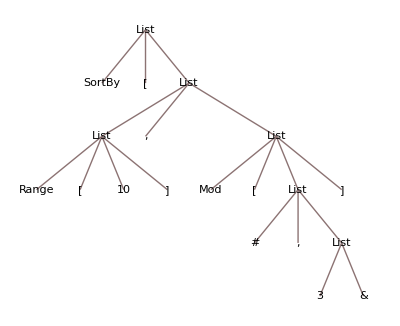

```mathematica
parseInput[mystring]//TreeForm
```

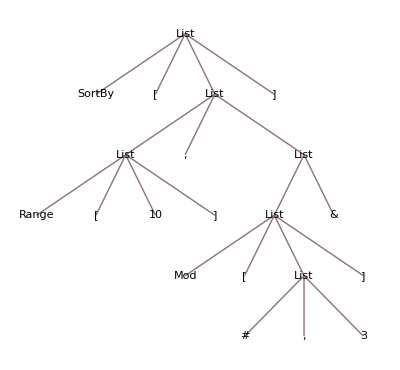

```mathematica
parseInput[mystring]//TreeForm
```

```mathematica
alllevels= getalllevels[mystring];alllevels//Column
```

{SortBy,[,List,]}
{List,,,List}
{Range,[,10,],List,&}
{Mod,[,List,]}
{#,,,3}

```mathematica
listA=Total/@Map[StringCount[#,"["]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
listB=Total/@Map[StringCount[#,"]"]&,alllevels,{2}]
```

{1,0,1,1,0}

```mathematica
Positive[listA-listB]
```

{False,False,False,False,False}

```mathematica
Negative[listA-listB]
```

{False,False,False,False,False}

```mathematica
MapThread[Greater,{listA,listB}]
```

{False,False,False,False,False}

#### Count the # arguments in functions:

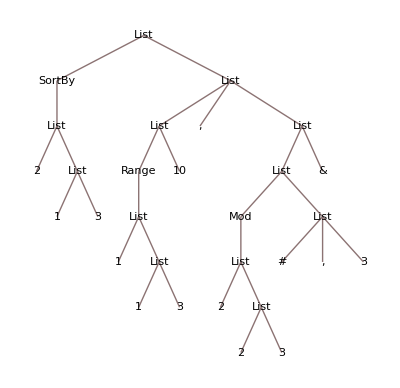

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> { function[{1+Length@Cases[","]@body,functionargs[function]}], body, lower}//TreeForm
```

#### Other stuff:

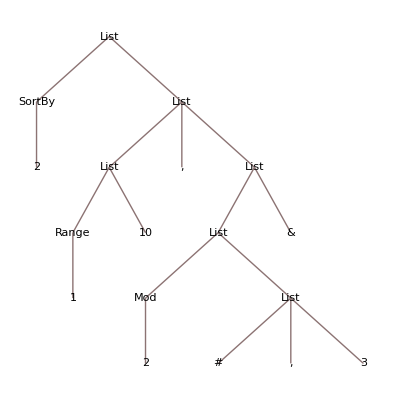

```mathematica
myexpr//. {upper___,function_,open_,body___,close_,lower___}/; open=="["&&close=="]"  :> {upper, function[1+Length@Cases[","]@body], body, lower}//TreeForm
```

```mathematica
(*/;Echo[{body,Length[body]},"Body Length"] *)
```

```mathematica
Cases[myexpr,{___,open_,body___,close_,___},Depth[myexpr]]//Column
```

{Range,[,10,]}
{#,,,3}
{Mod,[,{#,,,3},]}
{{Mod,[,{#,,,3},]},&}
{{Range,[,10,]},,,{{Mod,[,{#,,,3},]},&}}

10

## Back to Tim’s Idea:

### (* Convert an expression to a flattened String and try to build the tree correctly *)

#### Initialise:

```mathematica
mystring=makeExpressionString["SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]"]
```

"SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]"

```mathematica
SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]//Hold//TreeForm
```

#### Loop Over:

```mathematica
(* Trouble when a functions name is composed out of two other function names: eg IntegerPart -> Integet and Part are also funtions *)
```

```mathematica
(* Take the indexes of the functions that have a head which is a known function and are between brackets. Also they shouldn't include any subfunctions *)
```

```mathematica
(* Not[StringContainsQ[body,"Argument"]]&& *)
```

```mathematica
ranges=StringPosition[mystring,head__~~"["~~body___~~"]"
/; {head}==Names[head]
(*&&StringCases[body,xx__/;Names[xx]=={xx}]=={}*)
(*&& Names[body]== {}*)&&StringCount[body,"["]==StringCount[body,"]"],
Overlaps->All]; ranges//Column
```

{2,41}
{9,40}
{9,25}
{28,40}

#### From Giulio:

```mathematica
a[a[a[a[]]]]
```

a[a[a[a[]]]]

```mathematica
str="a[b[], foo[g[Plot[]]]]";
```

```mathematica
level=0;
head=None;
Reap[StringCases[str,{
"[":>Sow[Print["current head is: ", head];level++,"level"],
"]":>Sow[Print["current head is: ", head];level--,"level"],
h:LetterCharacter..:>Sow[head=h,"head"]}
];,_,Rule]
```

current head is: a

current head is: b

current head is: b

current head is: foo

current head is: g

current head is: Plot

current head is: Plot

current head is: Plot

«2 more identical outputs»

{Null,{head→{a,b,foo,g,Plot},level→{0,1,2,1,2,3,4,3,2,1}}}

```mathematica
Join[
Thread[StringPosition[str,"["][[All,1]]->1],
Thread[StringPosition[str,"]"][[All,1]]->-1]
]//KeySort
```

<|2→1,4→1,5→-1,9→1,11→1,13→1,14→-1,15→-1,16→-1,17→-1|>

```mathematica
Accumulate[Values@%]
```

{1,2,1,2,3,4,3,2,1,0}

```mathematica
Plus[Cos[1,2],3]
```

```mathematica
Plus[Cos[1],2,3]
```

```mathematica
Thread[StringPosition[str,"]"][[All,1]]->-1]
```

{5→-1,14→-1,15→-1,16→-1,17→-1}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

SortBy[Range[π argument], Mod[#1, 3 & ]]
Range[π argument], Mod[#1, 3 & ]
Range[π argument]
Mod[#1, 3 & ]

```mathematica
(* Count the arguments each function has *)
```

```mathematica
argnumbers=StringCount[functions,","]+1;argnumbers
```

{1,2}

```mathematica
(* Count the arguments each function should have *)
```

```mathematica
idealargnumbers=functionargs/@Flatten@StringCases[functions,head__ /; {head}==Names[head]:> head]
```

{{1,3},{2,3}}

```mathematica
(* Check if any of the functions has exactly the number of arguments that should be used as input *)
```

```mathematica
exactarguments=Table[{{argnumbers[[i]]}==(Range@@@idealargnumbers)[[i]]},{i,Length[argnumbers]}]//Flatten
```

{False,False}

```mathematica
(* When the arguments are exactly correct, replace with the the string "argument" so it doesn't get picked up again *)
```

```mathematica
(* TO DO: Find the Wolfram whay to do it *)
```

```mathematica
tempstring=mystring;
```

```mathematica
Do[tempstring=StringReplace[tempstring,functions[[ii]]/; exactarguments[[ii]]->"argument"],{ii,Length[argnumbers]}]
```

```mathematica
mystring=tempstring
```

"SortBy[Range[π argument], Mod[#1, 3 & ]]"

## Giulio 3/07

```mathematica
(*
```

```mathematica
level
```

```mathematica
inPartlevel
```

```mathematica
inString
```

```mathematica
inComment
```

```mathematica
{head,argcount,id}
```

```mathematica
j[[
```

```mathematica
[
```

```mathematica
]]
```

```mathematica
,
```

```mathematica
{"w",22->"]"}
```

```mathematica
{"w",-1->"]"}
```

```mathematica
f[[]
```

```mathematica
mystring
```

"SortBy[Range[π Argument], Mod[#1, 3 & ]]"

```mathematica
ranges=StringPosition[mystring,head__~~"["~~body___~~"]"/;Not[StringContainsQ[body,"Argument"]]&& {head}==Names[head]&&StringCases[body,xx__/;Names[xx]=={xx}]=={}&& Names[body]== {}&&StringCount[body,"["]==StringCount[body,"]"],Overlaps->All]; ranges//Column
```

{17,25}
{29,41}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

Cos[10.3]
Mod[#1, 3 & ]

```mathematica
Names["Range[IntegerPart[10.3]], Mod[#1, 3 & ]"]
```

{}

```mathematica
StringCases["Range[IntegerPart[10.3]], Mod[#1, 3 & ]",xx__/; Names[xx]=={xx}]
```

{Range,IntegerPart,Mod}

```mathematica
||Echo[{StringCases[body,xx__/;Names[xx]=={xx}],StringCount[body,"["],StringCount[body,"]"]}]
```

```mathematica
(* Delete the rest *)
```

```mathematica
ranges//Column
```

{17,25}
{29,41}

```mathematica
functions=StringTake[mystring,ranges];functions//Column
```

SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]]
SortBy[Range[π Cos[10.3]], Mod[#1, 3 & ]
SortBy[Range[π Cos[10.3]]
SortBy[Range[π Cos[10.3]
Range[π Cos[10.3]], Mod[#1, 3 & ]]
Range[π Cos[10.3]], Mod[#1, 3 & ]
Range[π Cos[10.3]]
Range[π Cos[10.3]
Cos[10.3]], Mod[#1, 3 & ]]
Cos[10.3]], Mod[#1, 3 & ]
Cos[10.3]]
Cos[10.3]
Mod[#1, 3 & ]]
Mod[#1, 3 & ]

```mathematica
StringCases["Range[π Cos[10.3]], Mod[#1, 3 & ]]","["~~"]"]
```

{}

```mathematica
<|2->{2,3},1->{ 3,4}|>
```

<|2→{2,3},1→{3,4}|>

```mathematica
%35[2]
```

{2,3}

## Before meeting with Tim:

Implement: {head, argcount, id}

```mathematica
str="a[b[],foo[g[Plot[]]]]";
```

```mathematica
str="a[b[cc[d[e[foo[t, h[x]]]]]]]";
```

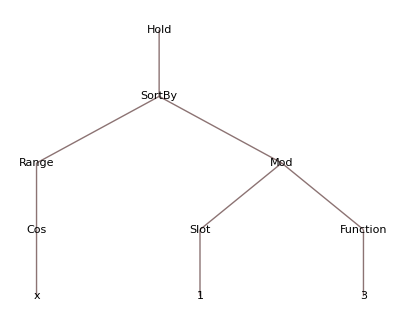

```mathematica
TreeForm@Hold@SortBy[Range[Cos[x]], Mod[#1, 3 & ]]
```

```mathematica
treestructure//SortBy[#[[1]]&]//Reverse//Dataset
```

Dataset[<>]

```mathematica
str="SortBy[Range[Cos[x]], Mod[#1, 3 & ]]"
```

SortBy[Range[Cos[x]], Mod[#1, 3 & ]]

Idea: The id should contain the current level + a unique id
previous head should be: Function Head: {level, unique id} ->  head, Current Number of Arguments, Key of parent Function

```mathematica
whatismyid[currentlevel_]:=Length@KeySelect[treestructure,#[[1]]==currentlevel&];
```

```mathematica
level=0;head=None;treestructure=<| |>;id=1;
Reap[StringCases[str,{
"[":>
Sow[Print[treestructure],
level++;
id=whatismyid[level];
treestructure=Append[{level,id+1}-> {head,1,If[level>1,(Keys@KeySelect[treestructure,#[[1]]==(level-1)&])[[-1]]]}]@treestructure;
Print["current level, head is: ",level," ", head];],
"]":>Sow[Print[treestructure],level--;
id=whatismyid[level];
If[level>0,head=treestructure[{level,id}][[3]]];Print["current level, head is: ",level," ", head];],
h:LetterCharacter..:>Sow[head=h,"head"],
",":> Sow[Print["A comma was found"];
id=whatismyid[level];
treestructure=Append[treestructure,{level,id}->{treestructure[{level,id}][[1]], treestructure[{level,id}][[2]]+1,treestructure[{level,id}][[3]]}]]}
];,_,Rule]
```

<||>

current level, head is: 1 SortBy

<|{1,1}→{SortBy,1,Null}|>

current level, head is: 2 Range

<|{1,1}→{SortBy,1,Null},{2,1}→{Range,1,{1,1}}|>

current level, head is: 3 Cos

<|{1,1}→{SortBy,1,Null},{2,1}→{Range,1,{1,1}},{3,1}→{Cos,1,{2,1}}|>

current level, head is: 2 {1,1}

<|{1,1}→{SortBy,1,Null},{2,1}→{Range,1,{1,1}},{3,1}→{Cos,1,{2,1}}|>

current level, head is: 1 Null

A comma was found

<|{2,1}→{Range,1,{1,1}},{3,1}→{Cos,1,{2,1}},{1,1}→{SortBy,2,Null}|>

current level, head is: 2 Mod

A comma was found

<|{2,1}→{Range,1,{1,1}},{3,1}→{Cos,1,{2,1}},{1,1}→{SortBy,2,Null},{2,2}→{Mod,2,{1,1}}|>

current level, head is: 1 Null

<|{2,1}→{Range,1,{1,1}},{3,1}→{Cos,1,{2,1}},{1,1}→{SortBy,2,Null},{2,2}→{Mod,2,{1,1}}|>

current level, head is: 0 Null

{Null,{head→{SortBy,Range,Cos,x,Mod},Null→{Null,Null,Null,Null,Null,Null,Null,Null},None→{<|{2,1}→{Range,1,{1,1}},{3,1}→{Cos,1,{2,1}},{1,1}→{SortBy,2,Null}|>,<|{2,1}→{Range,1,{1,1}},{3,1}→{Cos,1,{2,1}},{1,1}→{SortBy,2,Null},{2,2}→{Mod,2,{1,1}}|>}}}

## Function pattern matching from Tim

```mathematica
SyntaxInformation[AASTriangle]
```

```mathematica
{"ArgumentsPattern"->{_,_,_}}
```

```mathematica
symbolsWithInfo = GroupBy[Names["System`*"][[117;;]], Lookup[Association[SyntaxInformation[Symbol[#]]],"ArgumentsPattern"]=!={___}&]
```

```mathematica
Length@Names["System`*"][[117;;]]
```

6490

```mathematica
Length@symbolsWithInfo
```

6350

```mathematica
f[g[h[a,b,c],t]
```

```mathematica
symbolsSignatures = GroupBy[Names["System`*"][[117;;]], Lookup[Association[SyntaxInformation[Symbol[#]]],"ArgumentsPattern"]&]
```

```mathematica
{_,_.,_.,_.,_.}->{"CMYKColor","StableDistribution"}
```

```mathematica
?CMYKColor
```

```mathematica
{_,{__},OptionsPattern[]}
```

```mathematica
"BooleanRegion"
```

```mathematica
BooleanRegion[Xor,{Disk[{-1/3,0},1],Disk[{1/3,0},1]}]
```

```mathematica
...Multicolumn[Table[BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7]],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}],2]
```

```mathematica
...BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}...
```

```mathematica
MatchQ[{op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7],{op, {Or, And,¬#2∧#1&,#1⊻#2&}}
},{_,{__},OptionsPattern[]}]
```

False

```mathematica
BooleanRegion[op,{a,b}],PlotLabel-> …
```

```mathematica
BooleanRegion[op,{a,b},PlotLabel-> op],BaseStyle->…
```

```mathematica
BooleanRegion[op,{a,b},PlotLabel-> op,BaseStyle->Opacity[0.7]],{op, …
```

```mathematica
ToString[f["the string"],InputForm]
```

```mathematica
{"f","[","\"the string\"","]"}
```

```mathematica
{exp1,Nothing,exp13, exp2, Nothing}
```

{exp1,exp13,exp2}